```mathematica
Clear[z];
z[0,c_]=0;
z[n_,c_]:=z[n,c]=z[n-1,c]^2+c
```

```mathematica
Clear[m];
Clear[maxItr];
maxItr=500;
m[c_]:=Block[{ni=1},While[Abs[z[ni,c]]<2 && ni <maxItr,ni=ni+1]; ni]
```

```mathematica
Clear[mb];
mb=Table[m[x + ⅈ y],{x,-0.65,-0.4,0.001},{y,0.47,0.74,0.001}];
```

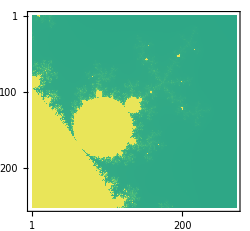

```mathematica
MatrixPlot[mb,ImageSize->250,ColorFunction->ColorData["BlueGreenYellow"]]
```

```mathematica
Export[NotebookDirectory[]<>"pics/ch04-mandelbrot.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/ch04-mandelbrot.pdf

```mathematica
(*Clear[mb2];*)
mb2=Table[m[x + ⅈ y],{x,-2,0.6,0.005},{y,-1.3,1.3,0.005}];//AbsoluteTiming
```

{191.262,Null}

```mathematica
MatrixPlot[mb2ᵀ,ImageSize->250,ColorFunction->"BlueGreenYellow",PlotLegends->False]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/ch04-mandelbrot-standard.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/ch04-mandelbrot-standard.pdf

```mathematica
MandelbrotSetPlot[ImageSize->250,PlotLabel->"Mandelbrot set",Frame->False]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/ch04-MandelbrotSetPlot.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/ch04-MandelbrotSetPlot.pdf

```mathematica
JuliaSetPlot[0.365-0.37ⅈ,ImageSize->250,PlotLabel->"Julia set",Frame->False,AspectRatio->1]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/ch04-JuliaSetPlot.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/ch04-JuliaSetPlot.pdf